```mathematica
Quit[];
```

## Load packages (run this)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$LoadFeynArts=True;
Global`$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
$FAVerbose = 0;

FAPatch[PatchModelsOnly->True];
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

args::shdw: Symbol args appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynArts 3.1 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.1.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Patching FeynArts models... done!

## Diagram and amplitude utilities (run this)

### Functions for generating diagrams

```mathematica
exclusions={V[1],V[2]};

frModelName="EFT_MeV_DM_scalar";
model={frModelName<>"/"<>frModelName};
genericModel={"Lorentz",frModelName<>"/"<>frModelName};

insertionLevel={Particles};
```

```mathematica
genDiags[inFields_,outFields_,nLoops_:0,adj_:{3,4,5},otherExclusions_:{}]:=Block[{tops},
tops=CreateTopologies[nLoops, Length[inFields]-> Length[outFields],ExcludeTopologies-> {Tadpoles,SelfEnergies,WFCorrections},Adjacencies-> adj];
InsertFields[tops,inFields-> outFields,InsertionLevel-> insertionLevel,Model-> model,GenericModel-> genericModel,ExcludeParticles-> Join[exclusions,otherExclusions]]
]
```

### Abbreviations for states

```mathematica
stateπ0=S[1];
stateπm=S[2];
stateπp=-S[2];
statek0=S[3];
statek0bar=-S[3];
statekm=S[4];
statekp=-S[4];
stateη=S[5];
stateγ=V[1];
stateρ=V[2];
stateν=F[1];
stateνbar=-F[1];
statel=F[2];
statelbar=-F[2];
statex=F[3];
statexbar=-F[3];
states=S[7];

mesonList={stateπ0,stateπp,stateπm,statekp,statekm,statek0,statek0bar,stateη};
```

### Function for creating amplitudes

Photon momentum should always be k

```mathematica
createAmp[diags_,inmomenta_,outmomenta_,lorentzIndices_,truncated_:False]:=Module[{amp},
(*Compute the diagram*)
amp=CreateFeynAmp[diags, PreFactor->-ⅈ,Truncated-> truncated,GaugeRules->{}];
amp=FCFAConvert[amp,
IncomingMomenta-> inmomenta,
OutgoingMomenta-> outmomenta,
LorentzIndexNames-> lorentzIndices,
LoopMomenta->{l}, 
UndoChiralSplittings->True,
List->False,
SMP-> True,
ChangeDimension-> 4,
FinalSubstitutions-> M$FACouplings,
TransversePolarizationVectors->{k}];

Simplify[ExpandScalarProduct[DiracSimplify[Contract[amp],DiracSubstitute67-> True]]]
]
```

### For writing to python files

```mathematica
dotProdsToStrings[expr_]:=expr//ReplaceAll[#,Pair[Momentum[pA_], Momentum[pB_]]:>ToExpression[ToString[pA]<>"DOT"<>ToString[pB]]]&
```

```mathematica
pyDir=NotebookDirectory[]<>"/python/";
```

### Set scalar’s gauge parameter to one

```mathematica
GaugeXi[S[7]]=1
```

1

### Substitute in for unstable mediator propagator

```mathematica
substituteUnstableSPropagator[expr_,moms_]:=expr/.FeynAmpDenominator[PropagatorDenominator[Total[Momentum/@moms], ms]]:>1/(SP[Total[Momentum/@moms]]-ms^2+ⅈ widths ms)//ScalarProductExpand
```

### Mandelstam t-> z

```mathematica
MandelstamtToz[Q_,m1_,m3_]:=Module[{E1,E3},
E1=(Q^2+m1^2-m3^2)/(2Q);E3=(Q^2-m1^2+m3^2)/(2Q);
m1^2+m3^2-2z √(E1^2-m1^2)√(E3^2-m3^2)
]
```

## Automation

```mathematica
MandelstamtToz[Q_,m1_,m3_]:=Module[{E1,E3},
E1=(Q^2+m1^2-m3^2)/(2Q);E3=(Q^2-m1^2+m3^2)/(2Q);
m1^2+m3^2-2z √(E1^2-m1^2)√(E3^2-m3^2)
]
```

```mathematica
ComputeAmplitudeSquared[states_,momenta_,masses_]:=Module[{diags,p1,p2,p3,p4,m1,m2,m3,m4,amp,ampSquared,E1,E3},
ClearScalarProducts[];

diags=genDiags[{states⟦1⟧,states⟦2⟧},{states⟦3⟧,states⟦4⟧}];
Paint[diags,ColumnsXRows->{1,1}];
p1=momenta⟦1⟧;m1=masses⟦1⟧;
p2=momenta⟦2⟧;m2=masses⟦2⟧;
p3=momenta⟦3⟧;m3=masses⟦3⟧;
p4=momenta⟦4⟧;m4=masses⟦4⟧;

amp=createAmp[diags,{p1,p2},{p3,p4},{μ,ν}];
amp=amp/.{FeynAmpDenominator[PropagatorDenominator[a_Momentum+b_Momentum,ms]]:>1/(SP[a+b,a+b]-ms^2+ⅈ widths ms),
FeynAmpDenominator[PropagatorDenominator[a_Momentum-b_Momentum,ms]]:>1/(SP[a-b,a-b]-ms^2+ⅈ widths ms),
FeynAmpDenominator[PropagatorDenominator[a_Momentum,ms]]:>1/(SP[a,a]-ms^2+ⅈ widths ms)};

SetMandelstam[Q^2,t,u,p1,p2,-p3,-p4,m1,m2,m3,m4];

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]]//ScalarProductExpand;
ampSquared=ampSquared//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->Tr]&;
ampSquared=ampSquared/.{u->m1^2+m2^2+m3^2+m4^2-Q^2-t}//Simplify;

E1=(Q^2+m1^2-m3^2)/(2Q);E3=(Q^2-m1^2+m3^2)/(2Q);
ampSquared/.{t->m1^2+m3^2-2z √(E1^2-m1^2)√(E3^2-m3^2)}
]
```

# χA→χA

## χ̄ χ→S S

### Compute Cross Section

```mathematica
ampSquaredxbarxtoss=Module[{fs,diags,amp,ampSquared},
ClearScalarProducts[];
SetMandelstam[Q^2,t,u,pxbar,px,-p1,-p2,mx,mx,ms,ms];

diags=genDiags[{statexbar,statex},{states,states}];

amp=createAmp[diags,{pxbar,px},{p1,p2},{μ,ν}]//PropagatorDenominatorExplicit;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum[#,ExtraFactor->1/4]&//ReplaceAll[#,DiracTrace->Tr]&//Contract;
ampSquared=ampSquared/.u->2(ms^2+mx^2)-Q^2-t;

1/2 ampSquared//Simplify(* since final state contains identical particles *)
];
```

```mathematica
$Assumptions={Q>0,1>4rx>0,1>4rs>0};

xSectIntegral2body[ampSquaredxbarxtoss,mx,ms,ms,Q];

%/.{mx->rx Q,ms->rs Q}//Simplify//StandardForm
```

1/(32 Q^2 (π-4 π rx^2))gsxx^4 (4 rs^2+4 rx^2-2 (1+√((-1+4 rs^2) (-1+4 rx^2)))+(4 (rs^2-4 rx^2)^2)/(1-2 rs^2+√((-1+4 rs^2) (-1+4 rx^2)))+(4 (rs^2-4 rx^2)^2)/(-1+2 rs^2+√((-1+4 rs^2) (-1+4 rx^2)))-2 (-1+2 rs^2+2 rx^2+√((-1+4 rs^2) (-1+4 rx^2)))-((1+6 rs^4+16 rx^2-32 rx^4-4 rs^2 (1+4 rx^2)) Log[-1/2 Q^2 (1-2 rs^2+√((-1+4 rs^2) (-1+4 rx^2)))])/(-1+2 rs^2)-((1+6 rs^4+16 rx^2-32 rx^4-4 rs^2 (1+4 rx^2)) Log[1/2 Q^2 (1-2 rs^2+√((-1+4 rs^2) (-1+4 rx^2)))])/(-1+2 rs^2)+((1+6 rs^4+16 rx^2-32 rx^4-4 rs^2 (1+4 rx^2)) Log[-1/2 Q^2 (-1+2 rs^2+√((-1+4 rs^2) (-1+4 rx^2)))])/(-1+2 rs^2)+((1+6 rs^4+16 rx^2-32 rx^4-4 rs^2 (1+4 rx^2)) Log[1/2 Q^2 (-1+2 rs^2+√((-1+4 rs^2) (-1+4 rx^2)))])/(-1+2 rs^2))

Need to simplify logs by hand

```mathematica
xSecxbarxtoss=1/(32 Q^2 (π-4 π rx^2))gsxx^4 (-4 √((1-4 rs^2) (1-4 rx^2))-(2 (rs^2-4 rx^2)^2 √((-1+4 rs^2) (-1+4 rx^2)))/(rs^4+rx^2-4 rs^2 rx^2)+((1+6 rs^4+16 rx^2-32 rx^4-4 rs^2 (1+4 rx^2)) Log[((-1+2 rs^2+√((-1+4 rs^2) (-1+4 rx^2)))/(1-2 rs^2+√((-1+4 rs^2) (-1+4 rx^2))))^2])/(-1+2 rs^2));
```

```mathematica
FortranForm[xSecxbarxtoss]>>(pyDir<>"xsec_xx_to_ss.py")
```

```mathematica
$Assumptions=True;
```

```mathematica
xSecxbarxtoss/.{rs->ms/√s,rx->mx/√s,Q->√s}//FullSimplify//ToString[#,FortranForm]&//StringReplace[#,{"Pi"->"M_PI","Sqrt"->"sqrt","Lam"->"lam","Log"->"log"}]&
```

(gsxx**4*((-2*sqrt(((-4*ms**2 + s)*(-4*mx**2 + s))/s**2)*(3*ms**4 - 16*ms**2*mx**2 + 2*mx**2*(8*mx**2 + s)))/(ms**4 - 4*ms**2*mx**2 + mx**2*s) + ((6*ms**4 - 32*mx**4 + 16*mx**2*s + s**2 - 4*ms**2*(4*mx**2 + s))*log((2*ms**2 + s*(-1 + sqrt(((-4*ms**2 + s)*(-4*mx**2 + s))/s**2)))**2/(-2*ms**2 + s + s*sqrt(((-4*ms**2 + s)*(-4*mx**2 + s))/s**2))**2))/((2*ms**2 - s)*s)))/(32.*M_PI*(-4*mx**2 + s))

```mathematica
(2 π^2 T)/((4π mx^2 T BesselK[2,mx/T])^2)/.{T->mx/x}//FullSimplify
```

x/(8 mx^5 (2x)^2)

### Expansion is ϵ

```mathematica
σVlabxbarxtoss=ComputeVelocityCrossSection[ampSquaredxbarxtoss,ms];
```

```mathematica
σVlabxbarxtoss//StandardForm
```

-(gsxx^4 (4 √ϵ+(2 (-4+r^2)^2 √ϵ)/(4-4 r^2+r^4+4 ϵ)+((3 r^4-8 r^2 (2+ϵ)+8 (3+6 ϵ+ϵ^2)) ArcTan[(2 √(-ϵ (1-r^2+ϵ)))/(2-r^2+2 ϵ)])/(√(-1+r^2-ϵ) (r^2-2 (1+ϵ)))))/(128 mx^2 √((ϵ (1+ϵ))/(1-r^2+ϵ)) (π+2 π ϵ))

```mathematica
ArcTan[ⅈ x]
```

ⅈ tanh^-1(x)

```mathematica
-(gsxx^4 (4 √ϵ+(2 (-4+r^2)^2 √ϵ)/(4-4 r^2+r^4+4 ϵ)+((3 r^4-8 r^2 (2+ϵ)+8 (3+6 ϵ+ϵ^2)) atanh[(2 √(ϵ (1+ϵ-r^2)))/(2(1+ϵ)-r^2)])/(√((1+ϵ)-r^2) (r^2-2 (1+ϵ)))))/(128 mx^2 √((ϵ (1+ϵ))/(1-r^2+ϵ)) (π+2 π ϵ))
```

```mathematica
σVlabxbarxtoss/.{ϵ->eps}//ToString[#,FortranForm]&//StringReplace[#,{"Pi"->"M_PI","Sqrt"->"sqrt","Lam"->"lam","Log"->"log","ArcTan"->"atan"}]&
```

-(gsxx**4*(4*sqrt(eps) + (2*sqrt(eps)*(-4 + r**2)**2)/(4 + 4*eps - 4*r**2 + r**4) + ((8*(3 + 6*eps + eps**2) - 8*(2 + eps)*r**2 + 3*r**4)*atan((2*sqrt(-(eps*(1 + eps - r**2))))/(2 + 2*eps - r**2)))/(sqrt(-1 - eps + r**2)*(-2*(1 + eps) + r**2))))/(128.*mx**2*(M_PI + 2*eps*M_PI)*sqrt((eps*(1 + eps))/(1 + eps - r**2)))

```mathematica
((2x)/BesselK[2,x]^2 ϵ^(1/2)(1+2ϵ)BesselK[1,2x √(1+ϵ)]//Series[#,{x,∞,0}]&//Normal)/.{ϵ->eps}//ToString[#,FortranForm]&//StringReplace[#,{"Pi"->"M_PI","Sqrt"->"sqrt","Lam"->"lam","Log"->"log","ArcTan"->"atan"}]&
```

E**((2 - 2*sqrt(1 + eps))*x)*((-3*sqrt(eps)*(1 + 2*eps)*(-1 + 20*sqrt(1 + eps))*sqrt(x))/(8.*(1 + eps)**0.75*sqrt(M_PI)) + (2*sqrt(eps)*(1 + 2*eps)*x**1.5)/((1 + eps)**0.25*sqrt(M_PI)))

```mathematica
((2x)/BesselK[2,x]^2 ϵ^(1/2)(1+2ϵ)BesselK[1,2x √(1+ϵ)]//Series[#,{x,∞,0},Assumptions->{ϵ>0}]&//Normal)//StandardForm
```

ⅇ^(x (2-2 √(1+ϵ))) ((2 x^(3/2) √ϵ (1+2 ϵ))/(√π (1+ϵ)^(1/4))-(3 √x √ϵ (1+2 ϵ) (-1+20 √(1+ϵ)))/(8 √π (1+ϵ)^(3/4)))

```mathematica
ⅇ^(x (2-2 √(1+ϵ))) ((2 x^(3/2) √ϵ (1+2 ϵ))/(√π (1+ϵ)^(1/4))-(3 √x √ϵ (1+2 ϵ) (-1+20 √(1+ϵ)))/(8 √π (1+ϵ)^(3/4)))/.{ϵ->1,x->50}//N
(2x)/BesselK[2,x]^2 ϵ^(1/2)(1+2ϵ)BesselK[1,2x √(1+ϵ)]/.{ϵ->1,x->50}//N

ⅇ^(x (2-2 √(1+ϵ))) ((2 x^(3/2) √ϵ (1+2 ϵ))/(√π (1+ϵ)^(1/4))-(3 √x √ϵ (1+2 ϵ) (-1+20 √(1+ϵ)))/(8 √π (1+ϵ)^(3/4)))/.{ϵ->10,x->100}//N
(2x)/BesselK[2,x]^2 ϵ^(1/2)(1+2ϵ)BesselK[1,2x √(1+ϵ)]/.{ϵ->10,x->100}//N
```

9.57398×10^-16

9.6074×10^-16

2.39061×10^-197

2.39273×10^-197

```mathematica
ⅇ^(x (2-2 √(ϵ+1))) ((2 x^(3/2) √ϵ (2 ϵ+1))/(√π (ϵ+1)^(1/4))-(3 √x √ϵ (2 ϵ+1) (20 √(ϵ+1)-1))/(8 √π (ϵ+1)^(3/4)))/.{x->10,ϵ->1}//
```

ⅇ^(10 (2-2 √2)) (60 2^(1/4) √(5/π)-(9 (20 √2-1) √(5/π))/(8 2^(1/4)))

## χπ→χ π

### χ π^±

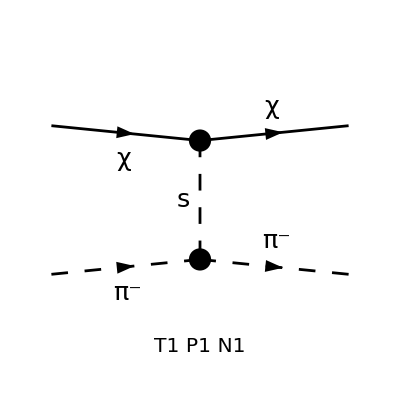

(gsxx^2 (2 z (Q^2/4-mx^2)+2 mx^2) (b0 (mdq+muq) (4 gsGG vs+9 Lam) (27 gsff^2 Lam^2 vs (4 gsGG vs+3 Lam)+gsff (48 gsGG^2 Lam vh vs^2-81 Lam^3 vh)-2 gsGG vh^2 (8 gsGG^2 vs^2-30 gsGG Lam vs+27 Lam^2))+162 gsGG Lam^3 vh^2 (2 mpi^2+2 z (Q^2/4-mx^2)-2 mx^2))^2)/(6561 Lam^6 vh^4 (4 gsGG vs+9 Lam)^2 (ms^4+ms^2 (widths^2-2 (2 mx^2-2 z (Q^2/4-mx^2)))+(2 mx^2-2 z (Q^2/4-mx^2))^2))

```mathematica
ElasticMSqrdDMChargedPion= ComputeAmplitudeSquared[{statex,stateπm,statex,stateπm},{pxi,pπi,pxf,pπf},{mx,mpi,mx,mpi}]
```

```mathematica
Integrate[ElasticMSqrdDMChargedPion,{z,-1,1}]
```

$Aborted

### χ π^0

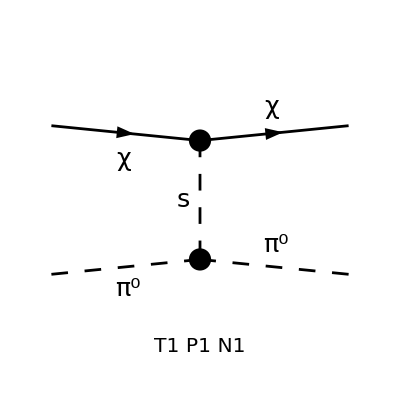

(gsxx^2 (2 z (Q^2/4-mx^2)+2 mx^2) (b0 (mdq+muq) (4 gsGG vs+9 Lam) (27 gsff^2 Lam^2 vs (4 gsGG vs+3 Lam)+gsff (48 gsGG^2 Lam vh vs^2-81 Lam^3 vh)-2 gsGG vh^2 (8 gsGG^2 vs^2-30 gsGG Lam vs+27 Lam^2))+162 gsGG Lam^3 vh^2 (2 mpi0^2+2 z (Q^2/4-mx^2)-2 mx^2))^2)/(6561 Lam^6 vh^4 (4 gsGG vs+9 Lam)^2 (ms^4+ms^2 (widths^2-2 (2 mx^2-2 z (Q^2/4-mx^2)))+(2 mx^2-2 z (Q^2/4-mx^2))^2))

```mathematica
ComputeAmplitudeSquared[{statex,stateπ0,statex,stateπ0},{pxi,pπ0i,pxf,pπ0f},{mx,mpi0,mx,mpi0}]
```

## χ̄ χ→ℓ̄ ℓ

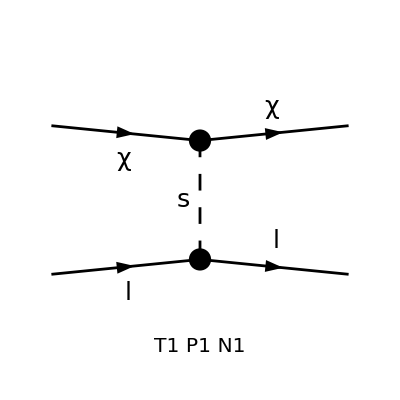

-(2 gsll^2 gsxx^2 (-2 z (Q^2/4-mx^2)-2 mx^2) (4 ml^2+2 z (Q^2/4-mx^2)-2 mx^2))/(ms^4+ms^2 (widths^2-2 (2 mx^2-2 z (Q^2/4-mx^2)))+(2 mx^2-2 z (Q^2/4-mx^2))^2)

```mathematica
ComputeAmplitudeSquared[{statex,statel,statex,statel},{pxi,pli,pxf,plf},{mx,ml,mx,ml}]
```

## χ̄ χ→γ γ

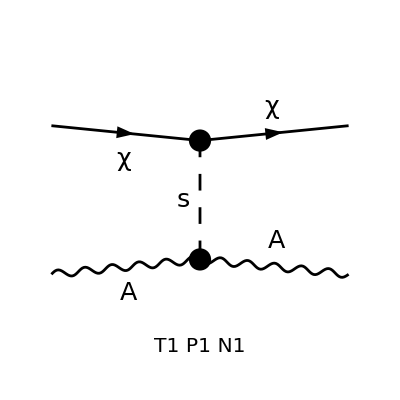

-(alphaEM^2 gsFF^2 gsxx^2 (4 mx^2 (z-1)-Q^2 z) (4 mx^2 (z+1)-Q^2 z) (4 mx^2 (z+1)-Q^2 z-t))/(4 π^2 Lam^2 (4 ms^4+4 ms^2 (-4 mx^2 (z+1)+Q^2 z+widths^2)+(Q^2 z-4 mx^2 (z+1))^2))

```mathematica
1/2ComputeAmplitudeSquared[{statex,stateγ,statex,stateγ},{pxi,pγi,pxf,pγf},{mx,0,mx,0}]//DoPolarizationSums[#,pγf,0]&//DoPolarizationSums[#,pγi,0]&//Simplify
```